```mathematica
expr1 = (π^2 α^2 ϵ^2 (2 ϵ^2-3 λ^2)+4 λ^2 (ϵ^2-2 λ^2))/(2 (ϵ-λ) (λ+ϵ) (π^2 α^2 ϵ^2+4 λ^2))
```

(π^2 α^2 ϵ^2 (2 ϵ^2-3 λ^2)+4 λ^2 (ϵ^2-2 λ^2))/(2 (ϵ-λ) (λ+ϵ) (π^2 α^2 ϵ^2+4 λ^2))

-Graphics-

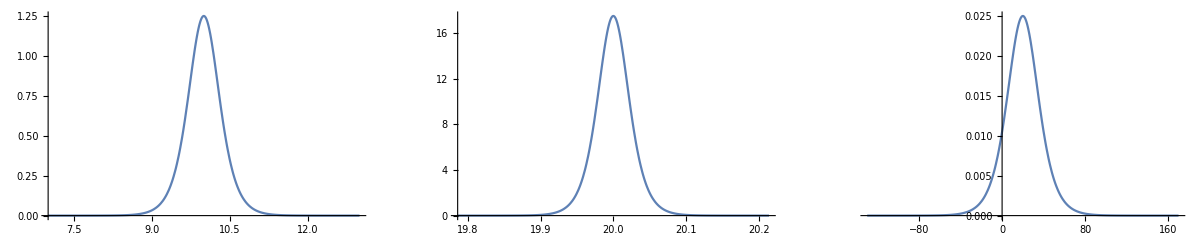

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϵp near {ϵp} = {0.0344}. NIntegrate obtained 0.980793 and 4.12605×10^-6 for the integral and error estimates.

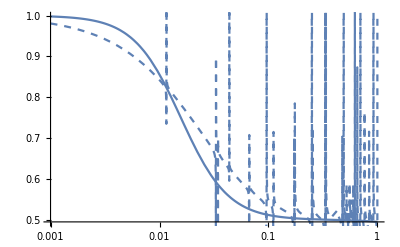

```mathematica
h[ϵ_,μ_,β_]:=(β Exp[β(ϵ-μ)])/(1+Exp[β(ϵ-μ)])^2
Plot[h[ϵ,10,5],{ϵ,(10-15/5),(10+15/5)},PlotRange->Full];
Plot[h[ϵ,20,70],{ϵ,(20-15/70),(20+15/70)},PlotRange->Full];
Plot[h[ϵ,20,0.1],{ϵ,(20-15/0.1),(20+15/0.1)},PlotRange->Full];

GraphicsRow[{%%%,%%,%}]

nsub = {α->0.001};
newexpr[μ_,β_]:=Block[{range},range={μ-15/β,μ+15/β};NIntegrate[h[ϵp,μ,β]expr1/.ϵ->ϵp/.nsub,{ϵp,range[[1]],range[[2]]}]]

LogLinearPlot[expr1/.ϵ->μ/.nsub/.μ->10,{λ,10^-3,10^0}];
LogLinearPlot[Table[newexpr[10,β],{β,{0.1}}],{λ,10^-3,10^0},PlotStyle->Dashed];
Show[%%,%]
```

```mathematica
pnts=Reap[NIntegrate[1/Sqrt[x],{x,0,1},Method->{"GlobalAdaptive","SingularityHandler"->{IMT,"TuningParameters"->1}},PrecisionGoal->2,EvaluationMonitor:>Sow[x]]][[2,1]];
ListPlot[Transpose[{pnts,Range[Length[pnts]]}]]
```

```mathematica
myexpr1 [μ_,β_,λ_,α_]:=Block[{tmp,range,λp},λp=λ;
	range ={μ-15/β,μ+15/β};
	tmp = (β Exp[β(ϵ-μ)])/(1+Exp[β(ϵ-μ)])^2(π^2 α^2 ϵ^2 (2 ϵ^2-3 λ^2)+4 λ^2 (ϵ^2-2 λ^2))/(2 (ϵ-λ) (λ+ϵ) (π^2 α^2 ϵ^2+4 λ^2));
	NIntegrate[tmp,{ϵ,range[[1]],range[[2]]},Exclusions->{λp,-λp},MaxRecursion->4]
]

myexpr [μ_,β_,λ_,α_]:=Block[{tmp,range,λp},λp=λ;
	range ={μ-15/β,μ+15/β};
	tmp = (β Exp[β(ϵ-μ)])/(1+Exp[β(ϵ-μ)])^2(π^2 α^2 ϵ^2 (2 ϵ^2-3 λ^2)+4 λ^2 (ϵ^2-2 λ^2))/(2 (ϵ-λ) (λ+ϵ) (π^2 α^2 ϵ^2+4 λ^2));
	NIntegrate[tmp,{ϵ,range[[1]],range[[2]]}]
]

matsubaraexpr = Block[{tmp,range,λp,residues},
	range ={μ-15/β,μ+15/β};
	tmp = (β Exp[β(ϵ-μ)])/(1+Exp[β(ϵ-μ)])^2(π^2 α^2 ϵ^2 (2 ϵ^2-3 λ^2)+4 λ^2 (ϵ^2-2 λ^2))/(2 (ϵ-λ) (λ+ϵ) (π^2 α^2 ϵ^2+4 λ^2));
	residues = residues = Join[Table[μ+(ⅈ π (2 n+1))/β,{n,1,100}]];
	Sum[ⅈ π Residue[tmp,{ϵ,ϵp}],{ϵp,residues}]
];

myexpr2 [μp_,βp_,λp_,αp_]:=matsubaraexpr/.{μ->μp,β->βp,λ->λp,α->αp}

(*myexpr[10,1,0.001,0.001]
myexpr[10,1,0.1,0.001]
*)
(*LogLinearPlot[{myexpr1[10,0.1,λ,0.001],myexpr[10,0.1,λ,0.001],Re[myexpr2[10,0.1,λ,0.001]]},{λ,10^-3,10^0},PlotStyle->{Black,Dashed,Dotted}]
*)
```

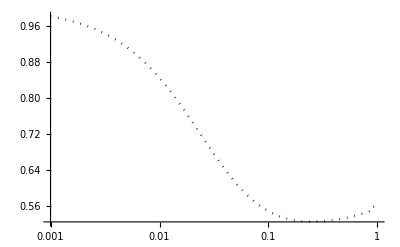

NIntegrate::zeroregion: Integration region (-0.00100014 | -0.0010001411255293980381853063254145021741085307750921989056185841606) cannot be further subdivided at the specified working precision. NIntegrate assumes zero integral there and on any further indivisible regions.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::inumri: The integrand (0.05 ⅇ^(0.1 (-10+ϵ)) (4.00113×10^-6 (-2.00056×10^-6+ϵ^2)+9.8696×10^-6 ϵ^2 (-3.00085×10^-6+2 ϵ^2)))/((1+ⅇ^(0.1 (-10+ϵ)))^2 (-0.00100014+ϵ) (0.00100014+ϵ) (4.00113×10^-6+9.8696×10^-6 ϵ^2)) has evaluated to Overflow, Indeterminate, or Infinity for all sampling points in the region with boundaries (-0.0010001411255293980381853063254145021741085307750921989056185841606 | -0.0010001411255293980395670286034297819357938130524832380094927418142).

NIntegrate::zeroregion: Integration region (-0.00100014 | -0.0010001411255293980381853063254145021741085307750921989056185841606) cannot be further subdivided at the specified working precision. NIntegrate assumes zero integral there and on any further indivisible regions.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::inumri: The integrand (0.05 ⅇ^(0.1 (-10+ϵ)) (4.00113×10^-6 (-2.00056×10^-6+ϵ^2)+9.8696×10^-6 ϵ^2 (-3.00085×10^-6+2 ϵ^2)))/((1+ⅇ^(0.1 (-10+ϵ)))^2 (-0.00100014+ϵ) (0.00100014+ϵ) (4.00113×10^-6+9.8696×10^-6 ϵ^2)) has evaluated to Overflow, Indeterminate, or Infinity for all sampling points in the region with boundaries (-0.0010001411255293980381853063254145021741085307750921989056185841606 | -0.0010001411255293980395670286034297819357938130524832380094927418142).

NIntegrate::zeroregion: Integration region (-0.00100014 | -0.0010001411255293980381853063254145021741085307750921989056185841606) cannot be further subdivided at the specified working precision. NIntegrate assumes zero integral there and on any further indivisible regions.

General::stop: Further output of NIntegrate::zeroregion will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::inumri: The integrand (0.05 ⅇ^(0.1 (-10+ϵ)) (4.00113×10^-6 (-2.00056×10^-6+ϵ^2)+9.8696×10^-6 ϵ^2 (-3.00085×10^-6+2 ϵ^2)))/((1+ⅇ^(0.1 (-10+ϵ)))^2 (-0.00100014+ϵ) (0.00100014+ϵ) (4.00113×10^-6+9.8696×10^-6 ϵ^2)) has evaluated to Overflow, Indeterminate, or Infinity for all sampling points in the region with boundaries (-0.0010001411255293980381853063254145021741085307750921989056185841606 | -0.0010001411255293980395670286034297819357938130524832380094927418142).

General::stop: Further output of NIntegrate::inumri will be suppressed during this calculation.

-Graphics-

```mathematica
myexpr1 [μ_,β_,λ_,α_]:=Block[{tmp,range,λp},λp=λ;
	range ={μ-15/β,μ+15/β};
	tmp = (β Exp[β(ϵ-μ)])/(1+Exp[β(ϵ-μ)])^2(π^2 α^2 ϵ^2 (2 ϵ^2-3 λ^2)+4 λ^2 (ϵ^2-2 λ^2))/(2 (ϵ-λ) (λ+ϵ) (π^2 α^2 ϵ^2+4 λ^2));
	NIntegrate[tmp,{ϵ,range[[1]],range[[2]]},Exclusions->{λp,-λp},MaxRecursion->16]
]
LogLinearPlot[{myexpr1[10,0.1,λ,0.001]},{λ,10^-3,10^0},PlotStyle->{Black,Dashed,Dotted}]
```

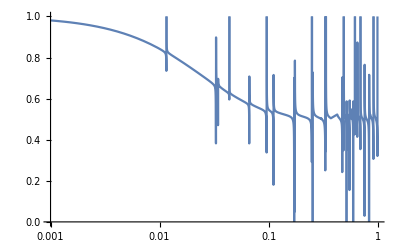

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϵp near {ϵp} = {0.0344}. NIntegrate obtained 0.980793 and 4.12605×10^-6 for the integral and error estimates.

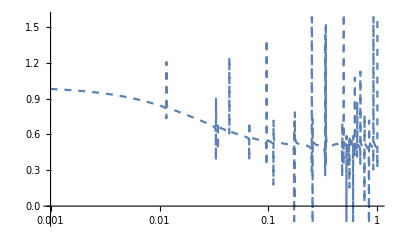

```mathematica
LogLinearPlot[Table[newexpr[10,β],{β,{0.1}}],{λ,10^-3,10^0},PlotStyle->Dashed]
```

```mathematica
{μ-15/β,μ+15/β}/.μ->10/.β->0.1
```

{-140.,160.}

```mathematica
LogLinearPlot[myexpr[10,0.1,0.01,0.001],{ϵ,9,11}]
```

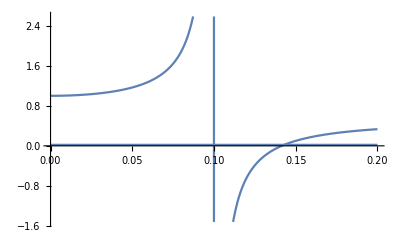

```mathematica
Plot[{(β Exp[β(ϵ-μ)])/(1+Exp[β(ϵ-μ)])^2,(π^2 α^2 ϵ^2 (2 ϵ^2-3 λ^2)+4 λ^2 (ϵ^2-2 λ^2))/(2 (ϵ-λ) (λ+ϵ) (π^2 α^2 ϵ^2+4 λ^2))}/.{μ->10,β->0.1,α->0.001,λ->0.1},{ϵ,0,0.2}]
```

```mathematica
(π^2 α^2 ϵ^2 (2 ϵ^2-3 λ^2)+4 λ^2 (ϵ^2-2 λ^2))/(2 (ϵ-λ) (λ+ϵ) (π^2 α^2 ϵ^2+4 λ^2))//Series[#,{ϵ,λ,2}]&
```

-λ/(4 (ϵ-λ))+(9 π^2 α^2+20)/(8 (π^2 α^2+4))+((-π^4 α^4+56 π^2 α^2-16) (ϵ-λ))/(16 (π^2 α^2+4)^2 λ)+((π^6 α^6-180 π^4 α^4+304 π^2 α^2+64) (ϵ-λ)^2)/(32 (π^2 α^2+4)^3 λ^2)+O((ϵ-λ)^3)

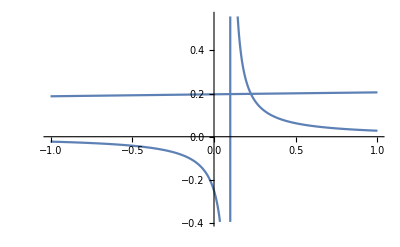

```mathematica
Plot[{10(β Exp[β(ϵ-μ)])/(1+Exp[β(ϵ-μ)])^2,λ/(4 (ϵ-λ))}/.{μ->10,β->0.1,α->0.001,λ->0.1},{ϵ,-1,1}]
```

```mathematica
Exp[(ϵ-μ+λ)]/(1+Exp[(ϵ-μ+λ)])^2 1/ϵ//Integrate[#,{ϵ,-∞,∞}]&
Exp[(ϵ-μ+λ)]/(1+Exp[(ϵ-μ+λ)])^2 1/ϵ-ⅇ^(λ+μ)/(ϵ (ⅇ^λ+ⅇ^μ)^2)//Series[#,{ϵ,0,2}]&
```

∫_(-∞)^∞ ⅇ^(λ-μ+ϵ)/(ϵ (ⅇ^(λ-μ+ϵ)+1)^2)ⅆϵ

(ⅇ^(λ+μ) (ⅇ^μ-ⅇ^λ))/((ⅇ^λ+ⅇ^μ)^3)+(ϵ ⅇ^(λ+μ) (-4 ⅇ^(λ+μ)+ⅇ^(2 λ)+ⅇ^(2 μ)))/(2 (ⅇ^λ+ⅇ^μ)^4)+(ϵ^2 ⅇ^(λ+μ) (11 ⅇ^(2 λ+μ)-11 ⅇ^(λ+2 μ)-ⅇ^(3 λ)+ⅇ^(3 μ)))/(6 (ⅇ^λ+ⅇ^μ)^5)+O(ϵ^3)

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϵ near {ϵ} = {1.22385×10^-226}. NIntegrate obtained 45029.6 and 37689.5 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϵ near {ϵ} = {-6.12065×10^-225}. NIntegrate obtained -45029.2 and 37689.5 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϵ near {ϵ} = {6.12065×10^-225}. NIntegrate obtained 45029.5 and 37689.5 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

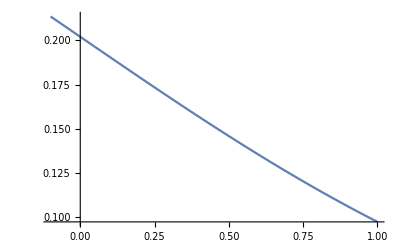

```mathematica
Plot[(Exp[(ϵ-0.5)]/(1+Exp[(ϵ-0.5)])^2 1/ϵ//NIntegrate[#,{ϵ,-5,-Δ},Exclusions->{ϵ==0}]&)+(Exp[(ϵ-0.5)]/(1+Exp[(ϵ-0.5)])^2 1/ϵ//NIntegrate[#,{ϵ,Δ,5},Exclusions->{ϵ==0}]&),{Δ,-0.1,1}]
```

### matsubara frequencies

```mathematica
residues = Join[{λ,-λ},Table[ⅈ π ((3n+1)μ/β),{n,1,15}]];
Sum[ⅈ π Residue[(β Exp[β(ϵ-μ)])/(1+Exp[β(ϵ-μ)])^2(π^2 α^2 ϵ^2 (2 ϵ^2-3 λ^2)+4 λ^2 (ϵ^2-2 λ^2))/(2 (ϵ-λ) (λ+ϵ) (π^2 α^2 ϵ^2+4 λ^2)),{ϵ,ϵp}],{ϵp,residues}]/.nsubst
```

0.-0.0199519 ⅈ

```mathematica
residues
```

{λ,-λ,(4 ⅈ π μ)/β,(7 ⅈ π μ)/β,(10 ⅈ π μ)/β,(13 ⅈ π μ)/β,(16 ⅈ π μ)/β,(19 ⅈ π μ)/β,(22 ⅈ π μ)/β,(25 ⅈ π μ)/β,(28 ⅈ π μ)/β,(31 ⅈ π μ)/β,(34 ⅈ π μ)/β,(37 ⅈ π μ)/β,(40 ⅈ π μ)/β,(43 ⅈ π μ)/β,(46 ⅈ π μ)/β}